```mathematica
n1[x_]:=Piecewise[{{1, Abs[x] ≤ 1/2}},0]
```

```mathematica
n1[x]
```

Piecewise[{{1, Abs[x]≤1/2}, {0, True}}]

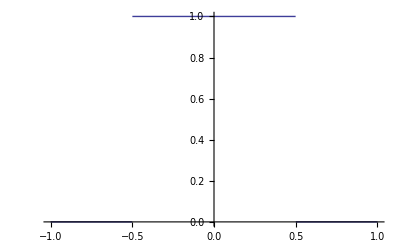

```mathematica
Plot[n1[x], {x, -1, 1}]
```

```mathematica
FourierTransform[n1[x], x, xi]
```

(√(2/π) Sin[xi/2])/xi

```mathematica
%^2
```

(2 Sin[xi/2]^2)/(π xi^2)

```mathematica
n2[x_]:=Convolve[n1[t], n1[t], t, x]
```

```mathematica
n2[x]
```

Piecewise[{{1-x, 0<x<1}, {1+x, -1<x≤0}, {0, True}}]

```mathematica
FourierTransform[n2[x], x, xi]
```

(2-2 Cos[xi])/(√(2 π) xi^2)